# Adaptive human behavior in epidemics on networks

Authors: Baltazar Espinoza (1,*), Jimmy Calvo Monge (2), Fabio Sanchez (2,3), Madhav Marathe (1).

1. Biocomplexity Institute and Initiative, Network Systems Science and Advanced Computing Division, University of Virginia, Virginia, USA
2. Escuela de Matematica, Universidad de Costa Rica, Ciudad Universitaria Rodrigo Facio, San Jose, 11501, Costa Rica
3. Centro de Investigacion en Matematica Pura y Aplicada, Universidad de Costa Rica, Ciudad Universitaria Rodrigo Facio, San Jose, 11501, Costa Rica

November 2023

## Utils

Infected Neighbors

```mathematica
(*This function returns the number and the list of infected neighbors of a given node*)

infneighs[ntwk_,nodeid_,neighsize_,ilist_]:=
Module[{ntw=ntwk,node=nodeid, ns=neighsize},

inf=Flatten@Position[ilist,1];

neighlist=IncidenceList[ntw,node,ns][[;;,2]];(*Delete[VertexList@NeighborhoodGraph[ntw,node,ns],1];*)

Do[
 ids=MemberQ[inf,#]&/@neighlist;

pos=Flatten[Position[ids,True]];

infneigh=neighlist[[#]]&/@ pos;

,{r,1,Length[neighlist]}
];

Return[{node,Length[infneigh],infneigh}]
]
```

Node maximizer

```mathematica
(*Single peak function*)
fs[x_,y_,z_]:=(x z -z^2)^y

(* The maxer code runs the optimization process for each vertex *)
vertxmaxer[ntwk_,nodeid_,dispars_,u_,neis_]:=
Module[{
ntw=ntwk, (* network used *)
node=nodeid[[1]], maxed=nodeid[[2]], (* the node for which the maximizer is running and the information about inf neghbours *)
β=dispars[[1]],γ=dispars[[2]], (*disease parameters*)
ν = u[[1]],T=u[[2]],(*time horizon*)
ns=neis (* Neighboorhood size to get the local prevalence*)
},

b=2*maxed; (* maximum possible # of edges for the utility function, the optimal utility is assumed at half of this*)
δ=0.99986; (*discount factor*)

(* Vector storing the optimal s utility *)
EUS=Table[0,{t,1,T+1}];

(* The last step in s assumes to use all edges *)
EUS[[-1]]=fs[b,ν,maxed];

(* Vector storaging the optimal i utility *)
EUI=Table[0,{t,1,T+1}];

(* Vector storaging the optimal i utility *)
EUR=Table[0,{t,1,T+1}];

(* The last step in r assumes to use all edges *)
(*EUR[[-1]]=fs[b,ν,maxed];*)

(* Vector storing the optimal # of edges for the susceptible node during the planning horizon *)
nedgest=Table[0,{i,1,T+1}];

nedgest[[-1]]=maxed;

(*Pt is the probability of disease transmission along an edge during a single time step*)
Pt=β; Pir=γ;

(* Optimization procedure *)
For[t=T,t≥ 1,t--, (* Horizon times, this goes backwards *)

(* individual's utility starts at zero*)
maxu=0;

(*(* Reset the list of neighbors, to start the new optimization *)
newnodeneighs=nodeneighs;*)

(* Evaluating all the contact rates for susceptible individuals, all possible variable states *)
Do[

Psi=1-(1-Pt)^edgesd;

(* Evaluating the expected utilities *)

(*Utility gained by being currently susceptible*)
EUS[[t]]= fs[b,ν,edgesd] +δ((1-Psi) EUS[[t+1]]+Psi EUI[[t+1]]);

EUI[[t]]=(0)fs[b,ν,maxed]+ δ( (1-Pir) EUI[[t+1]]+Pir EUR[[t+1]] );

EUR[[t]]=fs[b,ν,maxed]+δ EUR[[t+1]];

(*Compare the new utility with the previous one, if it's bigger, then adapt the behavior *)
If[EUS[[t]]>maxu,nedgest[[t]]=edgesd;maxu=EUS[[t]]];

,{edgesd,maxed,1,-1}]
];
Clear[t];
Return[nedgest]
]
```

Mean over multiple epidemics - no behavior

```mathematica
episim[ntwk_,epidemics_, iterations_, dispars_]:=
Module[{
net = ntwk,
epis = epidemics,
it = iterations,
pi=dispars[[1]],pr=dispars[[2]], (*disease parameters*)
},

epidist=ParallelTable[

(*Declare infected, susceptible and recovered vectors*)
Clear[i,s];
i0=RandomInteger[n];
i=Table[If[k==i0,1,0],{k,1,n}];
s=Table[1,{k,1,n}]-i;
r=Table[0,{k,1,n}];

epi=Table[

(* # of infected neighboors per node *)
infn=AdjacencyMatrix[net].i; 
ninfp=1-(1-pi)^#&/@infn;

(*Newly infected nodes*)
x=RandomReal[1,n];
newinf=Boole[Thread[x≤ninfp]];
upi=Table[If[s[[k]]==1&&newinf[[k]]==1,1,0],{k,1,n}];

(*Update S and I vectors: after infections*)
inew=i+upi;
snew=s-upi;

y=RandomReal[1,n];
newrec=Boole[Thread[y≤pr]];

(*Update I and R vectors: after recovery*)
upr=Table[If[inew[[k]]==1&&newrec[[k]]==1,1,0],{k,1,n}];

rnew=r+upr;
inew=inew-upr;
 
(*Update variable vectors*)
s=snew; i=inew;r=rnew;

{Count[snew,1],Count[inew,1],Count[rnew,1]}

,{l,2,it}];

epi

,{k,1,epis}];

Return[epidist];
];
```

Mean over multiple epidemics - behavior

```mathematica
bepisim[ntwk_, epidemics_,iterations_,dispars_,u_,neis_]:=
Module[{
net = ntwk,
bepis = epidemics,
it = iterations,
pi=dispars[[1]],pr=dispars[[2]], (*disease parameters*)
v = u[[1]],T=u[[2]],(*time horizon*)
ns=neis (* Neighboorhood size to get the local prevalence*)
},

bepidist=ParallelTable[

(*Declare infected, susceptible and recovered vectors*)
Clear[i,s];
i0=RandomInteger[n];
i=Table[If[k==i0,1,0],{k,1,n}];
s=Table[1,{k,1,n}]-i;
r=Table[0,{k,1,n}];

rednet=net;

epib=Table[

(* # of infected neighboors per node *)
infn=AdjacencyMatrix[rednet].i; 
ninfp=1-(1-pi)^#&/@infn;

(*Newly infected nodes*)
x=RandomReal[1,n];
newinf=Boole[Thread[x≤ninfp]];
upi=Table[If[s[[k]]==1&&newinf[[k]]==1,1,0],{k,1,n}];

(*Update S and I vectors: after infections*)
inew=i+upi;
snew=s-upi;

y=RandomReal[1,n];
newrec=Boole[Thread[y≤pr]];

(*Update I and R vectors: after recovery*)
upr=Table[If[inew[[k]]==1&&newrec[[k]]==1,1,0],{k,1,n}];

rnew=r+upr;
inew=inew-upr;
 
(*Update variable vectors*)
s=snew; i=inew;r=rnew;

(* =-=-= The maximization process =-=-= *)

rednet=net; (*Define a dummy network: this is the network to play with*)

(*Get the info of all susceptible nodes at time t*)
sus=Flatten@Position[s,1];
infofsus=infneighs[net,#,ns,i]&/@sus;

		vuse = v[[#]] &/@ sus;
		Tuse = T[[#]] &/@ sus;

(*Get only the info of susceptible with  infected neighbours*)
susinfs=Table[If[infofsus[[k,2]]≠0,infofsus[[k]]],{k,1,Length@sus}]/.Null->Sequence[];

(* Use the maximizer to define how many edges to drop: it returns the number of edges to leave *)
redneighs=Table[vertxmaxer[net,susinfs[[k]],{pi,pr},{vuse[[k]],Tuse[[k]]},ns][[1]],{k,1,Length[susinfs]}];

(*Get the list of the form {susceptible  id,{list of infected neighbours to remove}}*)
list=Table[{susinfs[[k,1]],RandomSample[susinfs[[k,3]],susinfs[[k,2]]-redneighs[[k]]]},{k,1,Length[redneighs]}];

(*Create the list of all the edges to remove at time t: of the form {s,i-rem}*)
edgestorem=Flatten[
Table[
{list[[k,1]]<->#}&/@list[[k,2]]
,{k,1,Length@redneighs}]];

(*Drop edges from the network*)
rednet=EdgeDelete[rednet,edgestorem];

{Count[s,1],Count[i,1],Count[r,1],EdgeCount[rednet],
N@Mean[Length[IncidenceList[rednet,#]]&/@sus]}

,{l,2,it}];

epib

,{z,1,bepis}];

Return[bepidist];
];
```

Define the plots (Comparisons)

```mathematica
getplots[ntwk_, epidistribution_, bepidistribution_]:=
Module[{
net = ntwk,
epidist = epidistribution,
bepidist = bepidistribution
},

(*Infected population dynamics - classic model*)
tseries=epidist[[;;,;;,2]]/n;

(*Infected population dynamics - classic model*)
tseriesrec=epidist[[;;,;;,3]]/n;

(*Total number of edges in the network*)
edglist=bepidist[[;;,;;,4]]/EdgeCount[net];

(*Infected population dynamics - adaptive model*)
btseriesinf=bepidist[[;;,;;,2]]/n;

(*Susceptible population dynamics - adaptive model*)
btseriessus=bepidist[[;;,;;,1]]/n;

(*Recovered population dynamics - adaptive model*)
btseriesrec=bepidist[[;;,;;,3]]/n;

(*Susceptible inds. mean number of edges*)
susedglist=bepidist[[;;,;;,5]]/N@Mean@VertexDegree[net];

(*Static network disease dynamics*)
pconsti=ListLinePlot[{Mean@tseries,Mean@tseries+StandardDeviation[N@tseries],Mean@tseries-StandardDeviation[N@tseries]},Filling->{{1->{3}},1->{2}},PlotRange->All,PlotStyle->{Directive[Thick,Dashed],None,None},TicksStyle->Directive[Bold, 14]];

(*Adaptive network disease dynamics*)
pbehav=ListLinePlot[{Mean@btseriesinf+StandardDeviation[N@btseriesinf],Mean@btseriesinf,Mean@btseriesinf-StandardDeviation[N@btseriesinf]},Filling->{{2->{3}},2->{1}},PlotRange->All,PlotStyle->{None,Directive[Thick,Red],None},TicksStyle->Directive[Bold, 14]];

(*Total population activity dynamics*)
Miny = Min[Mean@susedglist-2*StandardDeviation[N@susedglist]];
popredplot=ListLinePlot[{Mean@edglist,Mean@edglist+StandardDeviation[N@edglist],Mean@edglist-StandardDeviation[N@edglist]},Filling->{{1->{3}},1->{2}},PlotStyle->{Directive[Thick,Black],None,None},TicksStyle->Directive[Bold, 14],PlotRange->{{0,100},{Miny, 1}}];

(*Avg.node specific activity dynamics*)
susredplot=ListLinePlot[{Mean@susedglist,Mean@susedglist+StandardDeviation[N@susedglist],Mean@susedglist-StandardDeviation[N@susedglist]},Filling->{{1->{3}},1->{2}},PlotStyle->{Directive[Thick,Dashed,Blue],None,None},TicksStyle->Directive[Bold, 14],PlotRange->{{0,50},{Miny, 1}}];

Return[{pconsti,pbehav, popredplot , susredplot}]
];
```

## Experiments

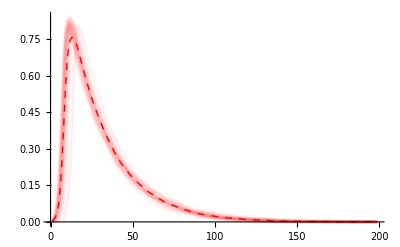

```mathematica
n=500; ped=0.05;
net=RandomGraph[BernoulliGraphDistribution[n,ped],VertexLabels->""];
epidist = episim[net, 40, 200, {0.05, 0.04}];
allplots=ListLinePlot[epidist[[;;,;;,2]]/n,PlotStyle->Directive[{Red,Opacity[0.025]}]];
meanplot=ListLinePlot[Mean@epidist[[;;,;;,2]]/n,PlotStyle->{Dashed,Red,Thick}];
plotnob=Show[allplots,meanplot]
```

Example with all nodes using the same adaptive parameters

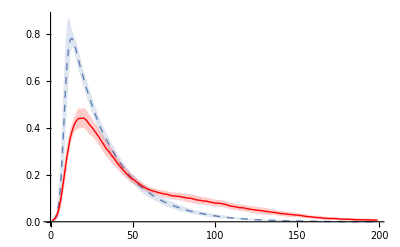

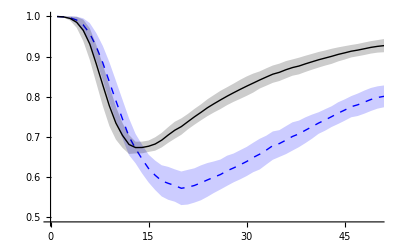

```mathematica
n=500; ped=0.05;
net=RandomGraph[BernoulliGraphDistribution[n,ped],VertexLabels->""];
vvector = Table[0.05, {k,1,n}];
Tvector = Table[7, {k,1,n}];
bepidist = bepisim[net, 20,100,{0.05,0.04},{vvector,Tvector},1];
{pconsti,pbehav, popredplot , susredplot} = getplots[net, epidist, bepidist];
Show[pconsti,pbehav]
Show[susredplot,popredplot]
```

```mathematica
tseries=epidist[[;;,;;,2]]/n;

(*Infected population dynamics - classic model*)
tseriesrec=epidist[[;;,;;,3]]/n;

(*Total number of edges in the network*)
edglist=bepidist[[;;,;;,4]]/EdgeCount[net];

(*Infected population dynamics - adaptive model*)
btseriesinf=bepidist[[;;,;;,2]]/n;

(*Susceptible population dynamics - adaptive model*)
btseriessus=bepidist[[;;,;;,1]]/n;

(*Recovered population dynamics - adaptive model*)
btseriesrec=bepidist[[;;,;;,3]]/n;

(*Susceptible inds. mean number of edges*)
susedglist=bepidist[[;;,;;,5]]/N@Mean@VertexDegree[net];

(*Static network disease dynamics*)
pconsti=ListLinePlot[{Mean@tseries,Mean@tseries+StandardDeviation[N@tseries],Mean@tseries-StandardDeviation[N@tseries]},Filling->{{1->{3}},1->{2}},PlotRange->All,PlotStyle->{Directive[Thick,Dashed],None,None},TicksStyle->Directive[Bold, 14]];

(*Adaptive network disease dynamics*)
pbehav=ListLinePlot[{Mean@btseriesinf+StandardDeviation[N@btseriesinf],Mean@btseriesinf,Mean@btseriesinf-StandardDeviation[N@btseriesinf]},Filling->{{2->{3}},2->{1}},PlotRange->All,PlotStyle->{None,Directive[Thick,Red],None},TicksStyle->Directive[Bold, 14]];

(*Total population activity dynamics*)
Miny = Min[Mean@susedglist-2*StandardDeviation[N@susedglist]];
popredplot=ListLinePlot[{Mean@edglist,Mean@edglist+StandardDeviation[N@edglist],Mean@edglist-StandardDeviation[N@edglist]},Filling->{{1->{3}},1->{2}},PlotStyle->{Directive[Thick,Black],None,None},TicksStyle->Directive[Bold, 14],PlotRange->{{0,100},{Miny, 1}}];

(*Avg.node specific activity dynamics*)
susredplot=ListLinePlot[{Mean@susedglist,Mean@susedglist+StandardDeviation[N@susedglist],Mean@susedglist-StandardDeviation[N@susedglist]},Filling->{{1->{3}},1->{2}},PlotStyle->{Directive[Thick,Dashed,Blue],None,None},TicksStyle->Directive[Bold, 14],PlotRange->{{0,50},{Miny, 1}}];
```

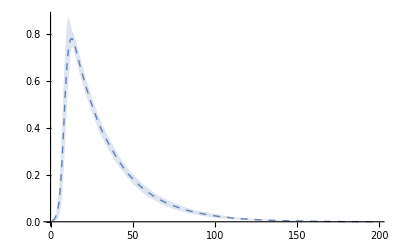

```mathematica
pconsti
```

```mathematica
n=500; ped=0.05;
net=RandomGraph[BernoulliGraphDistribution[n,ped],VertexLabels->""];
vvector = Table[0.05, {k,1,n}];
Tvector = Table[7, {k,1,n}]; (* Increase planning horizon *)
bepidist = bepisim[net, 2,200,{0.05,0.04},{vvector,Tvector},1];
{pconsti,pbehav, popredplot , susredplot} = getplots[net, epidist, bepidist];
Show[pconsti,pbehav]
Show[susredplot,popredplot]
```

Infected individuals dynamics / Behavioral response: population vs individual scale

```mathematica
(* Other plots: Individual adaptive response and susceptible nodes*)
(* pbehavsus=ListLinePlot[{Mean@btseriessus+StandardDeviation[N@btseriessus],Mean@btseriessus-StandardDeviation[N@btseriessus],Mean@btseriessus},Filling->{{3->{2}},3->{1}},PlotRange->All,PlotStyle->{None,None,Thick},TicksStyle->Directive[Bold, 14]];
Show[pbehavsus,susredplot,PlotRange->{{0,50},{0,1}}]
Show[susredplot,pbehav,PlotRange->{{0,50},{0,1}}] *)
```

Example with all nodes using distributions over adaptive parameters

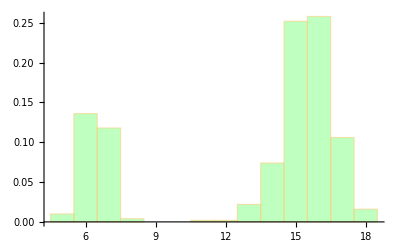

```mathematica
distT = MixtureDistribution[{1, 3}, {NormalDistribution[7, 0.5],NormalDistribution[16, 1] }];
TDist = Floor[#] &/@RandomVariate[distT, n];
Show[
 Histogram[TDist , 45, "ProbabilityDensity", ChartStyle -> {Opacity[.25,Green]}],
 Plot[PDF[TDist , x], {x, -2, 10}, PlotStyle -> PointSize[Medium]]]
```

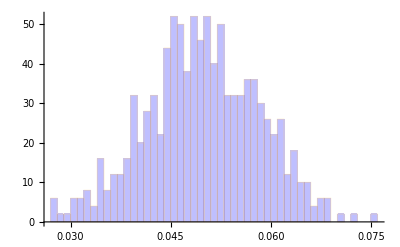

```mathematica
distV =NormalDistribution[0.05, 0.009];
VDist =  RandomVariate[distV,n];
Show[
 Histogram[VDist, 45, "ProbabilityDensity", ChartStyle -> {Opacity[.25,Blue]}],
 Plot[PDF[VDist, x], {x, -2, 10}, PlotStyle -> PointSize[Medium]]]
```

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

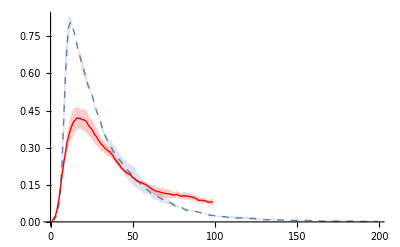

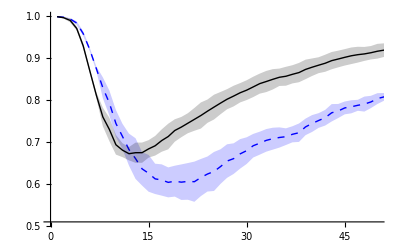

```mathematica
n=500; ped=0.05;
net=RandomGraph[BernoulliGraphDistribution[n,ped],VertexLabels->""];
bepidist2 = bepisim[net, 4,100,{0.05,0.04},{VDist,TDist},1];
{pconsti2,pbehav2, popredplot2 , susredplot2} = getplots[net, epidist, bepidist2];
Show[pconsti2,pbehav2]
Show[susredplot2,popredplot2] (*Behavioral response: population vs individual scale*)
```